# Test Rough Conductor Null Student-T

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

## Compare eval() and sample()

```mathematica
Run["clang++ -I include test/rough_conductor/test_rough_conductor_null_ST_eval_sample.cpp -O3 -o test/rough_conductor/test_rough_conductor_null_ST_eval_sample"]
```

0

```mathematica
roughness="0.7";
majorant="0.8";
gamma="2.8";
thetai="1.1";
eta=".5";
k="3.0";
```

```mathematica
argstr=roughness<>" "<>majorant<>" "<>gamma<>" "<>thetai<>" "<>eta<>" "<>k<>" 1000000 100 > test/rough_conductor/test_sample_eval.txt"
```

0.7 0.8 2.8 1.1 .5 3.0 1000000 100 > test/rough_conductor/test_sample_eval.txt

```mathematica
Run["./test/rough_conductor/test_rough_conductor_null_ST_eval_sample "<>argstr]
```

256

```mathematica
check=Import["test/rough_conductor/test_sample_eval.txt","Table"];
```

```mathematica
imEval=check[[-100;;-1]];
imSample=check[[2;;101]];
```

```mathematica
b=.5/Max[Flatten[imSample]];
gamma=0.3;
```

```mathematica
{Image[(b Abs[imEval])^gamma],Image[(b Abs[imSample])^gamma],(Image[(b Abs[imEval-imSample])^gamma])}
```

{-Graphics-,-Graphics-,-Graphics-}

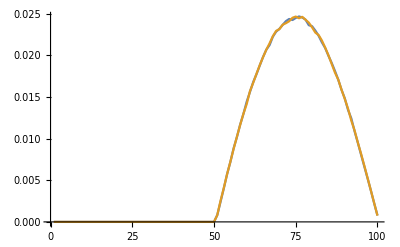

```mathematica
ListPlot[Total/@{Transpose[imSample],Transpose[imEval]},Joined->True]
```

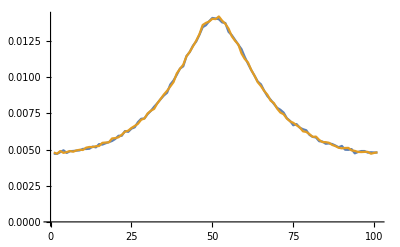

```mathematica
ListPlot[Total/@{imSample,imEval},Joined->True]
```